```mathematica
hbar=1.05457148×10(10)^-34; Delta = 9.2 10^12;Gam = 32.8 10^6/(2 Pi);λ = 852.1 10^-9; Inti = 60000000;mCs = (133 1.660 10^-27);Er = hbar^2 k^2/(2*mCs);
alal = 2;k= 2 Pi/λ;
el = 1.602 10^-19;
me = 9.1 10^-31;
λred = 852 10^-9;
γred = 32.8 10^6;
hp = hbar 2 Pi;
Ints = (Pi hp c γred)/(3 λred^3);
c=3 10^8;
```

```mathematica
Ωrabired[Int_]:= Sqrt[(3 λred^3 γred Int)/(2 Pi hp c)]; (*Rabi frequency red light*)
```

```mathematica
Int= 2 90 /Pi /(0.2)^2 10
```

14323.9

-------------------------------------------------------------------------------------------

```mathematica
Int= 2 90 /Pi /(0.2)^2 10;ΔR = 40 10^9;
```

```mathematica
Ωf = (Ωrabired[Int] Ωrabired[Int])/(2ΔR)
```

872428.

```mathematica
ΓR = (Ωf^2 Ωrabired[0.001 Int]^2)/(2 Ωf^2 γred^2+ Ωrabired[0.001 Int]^4)γred (*(in the Raman saturation regime)*)
```

54309.8

```mathematica
ΓRcarrier = (Ωrabired[0.0001 Int]^2/4)/(0+Ωrabired[0.0001Int]^2/2+γred^2/2)γred
```

105708.

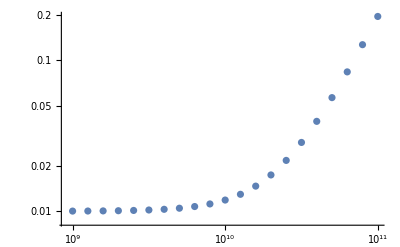

```mathematica
ListLogLogPlot[Table[With[{x:=10^ino},ΔR = 10^ino;
Ωf = (Ωrabired[Int] Ωrabired[Int])/(2ΔR);


{ΔR,(Ωrabired[0.00001 Int]^2/4)/(0+Ωrabired[0.00001Int]^2/2+γred^2/2)γred /((Ωf^2 Ωrabired[0.001 Int]^2)/(2 Ωf^2 γred^2+ Ωrabired[0.001 Int]^4)γred )}],{ino, 9, 11,0.1}]]
```

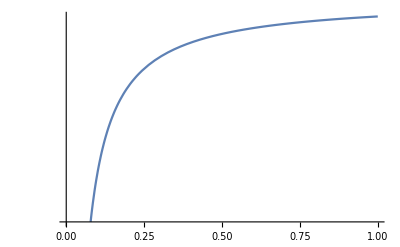

```mathematica
LogPlot[ΓRcarrier = (Ωrabired[ Int]^2/4)/(0+Ωrabired[Int]^2/2+γred^2/2)γred, {Int, 0, 10^8}]
```

```mathematica
4
```

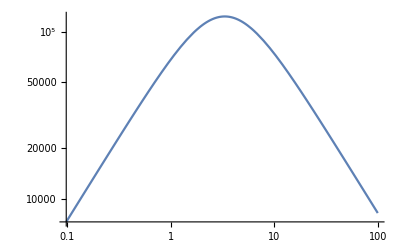

```mathematica
LogLogPlot[(Ωf^2 Ωrabired[Int]^2)/(2 Ωf^2 γred^2+ Ωrabired[ Int]^4)γred ,{Int,0,10^2}]
```